```mathematica
a=1;b=1;c=1; mmax=9;nmax=9;
f[x_,y_]:=(1/2)Sin[ Pi x ] Sin[8 Pi y]-(1/2)Sin[8 Pi x]Sin[Pi y]+3 Sin[4 Pi x] Sin[7 Pi y]- 3 Sin[7 Pi x ]Sin[4 Pi y];

lambda[i_,j_]:=Pi*Sqrt[(i/a)^2+(j/b)^2];





For[i=1,i<mmax,i++,
For[j=1,j<nmax,j++,
B[i,j]=Integrate[f[x,y]*Sin[(i*Pi*x)/a]*Sin[(j*Pi*y)/b],{x,0,a},{y,0,b}];
];
];

membrana[x_,y_,t_]=Sum[B[i,j]*Sin[i*Pi*x/a]*Sin[j*Pi*y/b]*Cos[c*lambda[i,j]*t],{i,1,mmax},{j,1,nmax}];
```

```mathematica
Manipulate[Plot3D[membrana[x,y,t],{x,0,a},{y,0,b},PlotRange->{{0,a},{0,b},{-1.6,1.6}},Mesh->15],{t,0,10,0.01}]
```

```mathematica
h=f[x,y]
```

-1/2 Sin[8 π x] Sin[π y]-3 Sin[7 π x] Sin[4 π y]+3 Sin[4 π x] Sin[7 π y]+1/2 Sin[π x] Sin[8 π y]

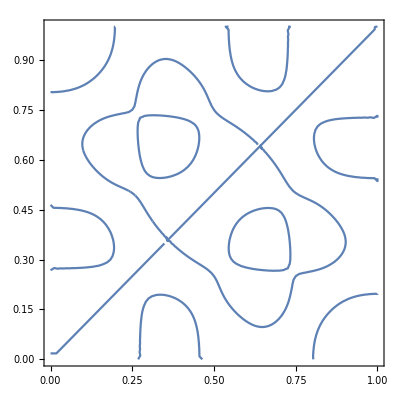

```mathematica
ContourPlot[h==0,{x,0,1},{y,0,1}]
```